# PLOTING FUNCTION WITH MATHEMATICA _Lecture-1_

## Created by : SchrodenBug

## Display a Simple plot

### Define a Simple Function and plot the output that function produces with the basic Plot[] command in Mathematica

Example:

1. Step 1! Define the function

```mathematica
f[x_]:= x^2
```

2. Step 2! plot the function

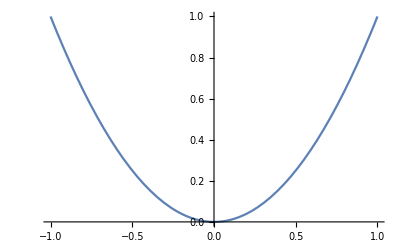

```mathematica
Plot[f[x],{x,-1,1}]
```

PS ! Optional Step! import Latex to For better text style

```mathematica
<<MaTeX`
```

3. Step 3! customize and add more information to your plot with options available in Mathematica (Title, Label, Color, ...)

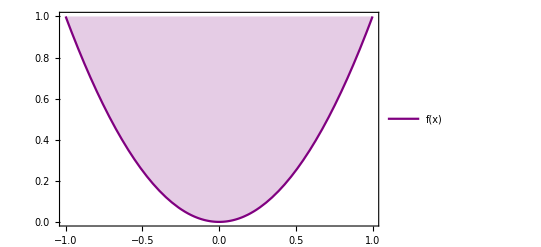

```mathematica
p1 = Plot[f[x],{x,-1,1}, Frame->True, FrameLabel->MaTeX@{" x", " f(x)"}, PlotLegends->"AllExpressions",PlotRange->{0,1}, PlotLabel->MaTeX@"\\text{f(x) = }"MaTeX@f[x], PlotStyle->{Purple}, FrameTicksStyle->Directive[Red,12], Filling->Top]
```

4. Step 4! export a plot together with its legend

```mathematica
Export["Plot.png", p1]
```

Plot.png

PS : The exported file will be found in the session’s working directory, see Directory, The working directory can be open directly from the notebook with The command

```mathematica
File@Directory[]
```

File[C:\Users\arfao\OneDrive\Documents]